{{0.812209},{0.26588},{1.79642},{1.60568}}

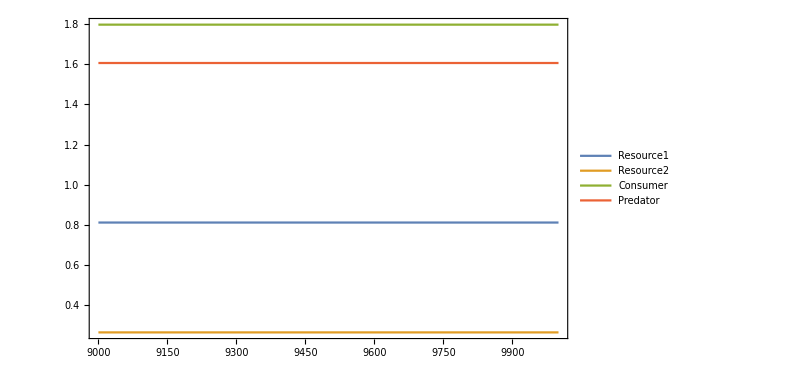

```mathematica
ClearAll["Global`*"];
r1=2;
K1=3;
r2=2;
K2=3;
A=1.0;
H=0.0000008;
B=0.11;
S1=1.0;
h1=0.6;
e1=0.11;
S2=0.4;
h2=1/3;
e2=0.2;
M=0.1;
d=0.1;

α=0;
p=0.1;

Tf = 10000;
eqs={
Res1'[t]==r1*Res1[t]*(1-Res1[t]/K1)-((A*p*Res1[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*(1-p)*Res1[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Res2'[t]==r2*Res2[t]*(1-Res2[t]/K2)-((A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*p*Res2[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*p*Res1[t]+B*A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-M*Con[t]-((S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*S1*(1-p)*Res1[t]+e1*S1*p*Res2[t]+e2*S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t]-d*Pred[t],
Res1[0]==1, Res2[0]==1, Con[0]==1, Pred[0]==1};
s = NDSolve[eqs, {Res1,Res2, Con, Pred, q},{t,0,Tf}];
Table[{Res1[t]/.s, Res2[t]/.s, Con[t]/.s, Pred[t]/.s}, {t, 9000, 10000, 0.01}]//Mean
Plot[
Evaluate[{Res1[t], Res2[t], Con[t],Pred[t]}/.s],
{t,9000,Tf},
PlotStyle->Automatic,
PlotLegends->{"Resource1", "Resource2", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All,
Frame->True]
```

#### Type II functional response

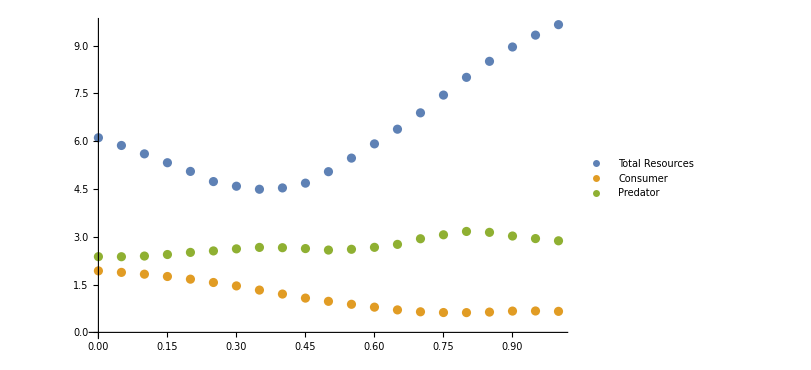

(0. | 5.4308 | 0.678037 | 1.93116 | 2.37662
0.05 | 4.97803 | 0.888055 | 1.88339 | 2.37459
0.1 | 4.45889 | 1.14347 | 1.82668 | 2.3957
0.15 | 3.85918 | 1.46519 | 1.75428 | 2.44379
0.2 | 3.21216 | 1.83998 | 1.67043 | 2.51072
0.25 | 2.41936 | 2.31372 | 1.56599 | 2.55679
0.3 | 1.79002 | 2.79699 | 1.45881 | 2.62142
0.35 | 1.10213 | 3.38992 | 1.32783 | 2.66707
0.4 | 0.570683 | 3.96286 | 1.20322 | 2.65798
0.45 | 0.132091 | 4.5512 | 1.07608 | 2.63026
0.5 | 0.0173242 | 5.02624 | 0.974976 | 2.58369
0.55 | 0.00614136 | 5.4632 | 0.881885 | 2.60822
0.6 | 0.0314342 | 5.88448 | 0.791982 | 2.66939
0.65 | 0.0891389 | 6.28735 | 0.705874 | 2.7621
0.7 | 0.324085 | 6.56578 | 0.646474 | 2.93855
0.75 | 0.764005 | 6.68298 | 0.62324 | 3.06288
0.8 | 1.29959 | 6.7041 | 0.620807 | 3.16805
0.85 | 1.86464 | 6.64169 | 0.637322 | 3.13964
0.9 | 2.43779 | 6.51857 | 0.668657 | 3.02422
0.95 | 2.81849 | 6.51025 | 0.672001 | 2.94393
1. | 3.0821 | 6.57511 | 0.660279 | 2.87412)

```mathematica
ClearAll["Global`*"];
r1=2;
K1=10;
r2=2;
K2=10;
A=1.0;
H=0.008;
B=0.11;
S1=1.0;
h1=0.7;
e1=0.11;
S2=0.39568;
h2=0.37096;
e2=0.5;
M=0.1;
d=0.1;

p=0.05;

Tf = 10000;

Tf = 10000;
eqs={
Res1'[t]==r1*Res1[t]*(1-Res1[t]/K1)-((A*p*Res1[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*(1-p)*Res1[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Res2'[t]==r2*Res2[t]*(1-Res2[t]/K2)-((A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*p*Res2[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*p*Res1[t]+B*A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-M*Con[t]-((S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*S1*(1-p)*Res1[t]+e1*S1*p*Res2[t]+e2*S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t]-d*Pred[t],
Res1[0]==1, Res2[0]==1, Con[0]==1, Pred[0]==1};

aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res1, Res2,Con, Pred},{t,0,Tf}];
Sow[
{i, Table[{Res1[t]/.sol, Res2[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 8000, 10000, 0.01}]//Mean}
];
,{i, 0,1, 0.05}
]
][[2,1]];
ListPlot[
{Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]]+aa[[n]][[2]][[2]][[1]]}, {n,1, 21}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[3]][[1]]},  {n,1, 21}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[4]][[1]]},  {n,1, 21}]},
PlotLegends->{"Total Resources", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All
]
MatrixForm[Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]], aa[[n]][[2]][[2]][[1]], aa[[n]][[2]][[3]][[1]], aa[[n]][[2]][[4]][[1]]}, {n,1, 21}]]
```

```mathematica
(4.65)/(6.1)
```

0.762295

```mathematica
aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res1, Res2,Con, Pred},{t,0,Tf}];
Sow[
{i, Table[{Res1[t]/.sol, Res2[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 8000, 10000, 0.01}]//Mean}
];
,{i, 0,1, 0.01}
]
][[2,1]]
Export["K:\\IGP exp_in lab\\ProgressReport_20171115\\Type2.csv",Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]], aa[[n]][[2]][[2]][[1]], aa[[n]][[2]][[3]][[1]], aa[[n]][[2]][[4]][[1]]}, {n,1, 101}]]
```

{{0.,{{5.19768},{0.432623},{2.03449},{2.86823}}},{0.01,{{5.2638},{0.457442},{2.02958},{2.75842}}},{0.02,{{5.23484},{0.492674},{2.02021},{2.73126}}},{0.03,{{5.18005},{0.533001},{2.01279},{2.69206}}},{0.04,{{5.16699},{0.566031},{2.00019},{2.69134}}},{0.05,{{5.01102},{0.625748},{1.98435},{2.69622}}},{0.06,{{4.96023},{0.666572},{1.97465},{2.68398}}},{0.07,{{4.86045},{0.717474},{1.95926},{2.70685}}},{0.08,{{4.72438},{0.780195},{1.94172},{2.71011}}},{0.09,{{4.63255},{0.834016},{1.92559},{2.70716}}},{0.1,{{4.54696},{0.889216},{1.91355},{2.7024}}},{0.11,{{4.42784},{0.952373},{1.89613},{2.72461}}},{0.12,{{4.35382},{1.00754},{1.88211},{2.71133}}},{0.13,{{4.15893},{1.09595},{1.85567},{2.76153}}},{0.14,{{4.01967},{1.16923},{1.84049},{2.73411}}},{0.15,{{3.95015},{1.22753},{1.82389},{2.74564}}},{0.16,{{3.82388},{1.30407},{1.80368},{2.76494}}},{0.17,{{3.64598},{1.39461},{1.77947},{2.78063}}},{0.18,{{3.43644},{1.50616},{1.74649},{2.82746}}},{0.19,{{3.40229},{1.56258},{1.73201},{2.85262}}},{0.2,{{3.17828},{1.67662},{1.70266},{2.85929}}},{0.21,{{3.06843},{1.76188},{1.68084},{2.88376}}},{0.22,{{2.88153},{1.87266},{1.65099},{2.90541}}},{0.23,{{2.7118},{1.98308},{1.62391},{2.91224}}},{0.24,{{2.54655},{2.09174},{1.59373},{2.94163}}},{0.25,{{2.42987},{2.19734},{1.56599},{2.97872}}},{0.26,{{2.26551},{2.30603},{1.5384},{2.98998}}},{0.27,{{2.18571},{2.40353},{1.51187},{3.03688}}},{0.28,{{1.97376},{2.52893},{1.48104},{3.02335}}},{0.29,{{1.81785},{2.65686},{1.44845},{3.04665}}},{0.3,{{1.7445},{2.74092},{1.42841},{3.05474}}},{0.31,{{1.59058},{2.87757},{1.39189},{3.08989}}},{0.32,{{1.38552},{3.02058},{1.35619},{3.08248}}},{0.33,{{1.29952},{3.13269},{1.32775},{3.11376}}},{0.34,{{1.14624},{3.25706},{1.29735},{3.10492}}},{0.35,{{1.0921},{3.36305},{1.27033},{3.149}}},{0.36,{{0.990531},{3.46925},{1.24559},{3.13717}}},{0.37,{{0.84497},{3.62527},{1.20408},{3.16918}}},{0.38,{{0.760012},{3.73658},{1.17828},{3.16984}}},{0.39,{{0.655698},{3.84846},{1.15141},{3.15956}}},{0.4,{{0.61239},{3.96165},{1.1236},{3.19533}}},{0.41,{{0.523886},{4.08159},{1.09467},{3.19559}}},{0.42,{{0.488357},{4.18424},{1.0699},{3.22205}}},{0.43,{{0.372031},{4.30676},{1.04106},{3.18828}}},{0.44,{{0.345562},{4.41243},{1.01576},{3.21785}}},{0.45,{{0.284196},{4.51492},{0.991877},{3.20863}}},{0.46,{{0.260756},{4.62095},{0.966693},{3.2381}}},{0.47,{{0.215752},{4.71716},{0.945076},{3.23559}}},{0.48,{{0.116684},{4.8707},{0.906656},{3.25846}}},{0.49,{{0.0919005},{4.96373},{0.885461},{3.25095}}},{0.5,{{0.0885315},{5.05064},{0.865823},{3.26434}}},{0.51,{{0.0870286},{5.1367},{0.846422},{3.27956}}},{0.52,{{0.0873363},{5.22189},{0.827262},{3.29657}}},{0.53,{{0.0893998},{5.30619},{0.808346},{3.31528}}},{0.54,{{0.0931642},{5.38959},{0.789675},{3.33565}}},{0.55,{{0.0985755},{5.47207},{0.771253},{3.35759}}},{0.56,{{0.10558},{5.55361},{0.75308},{3.38105}}},{0.57,{{0.114124},{5.63421},{0.73516},{3.40596}}},{0.58,{{0.124156},{5.71385},{0.717492},{3.43223}}},{0.59,{{0.135623},{5.79252},{0.700077},{3.45982}}},{0.6,{{0.170556},{5.85343},{0.68735},{3.50044}}},{0.61,{{0.265793},{5.87345},{0.685279},{3.54207}}},{0.62,{{0.326804},{5.92043},{0.676068},{3.57319}}},{0.63,{{0.369911},{5.9709},{0.66598},{3.59435}}},{0.64,{{0.434365},{6.01654},{0.656463},{3.64253}}},{0.65,{{0.449337},{6.08931},{0.641543},{3.6442}}},{0.66,{{0.512795},{6.12032},{0.636039},{3.67973}}},{0.67,{{0.575605},{6.14907},{0.631637},{3.70667}}},{0.68,{{0.616306},{6.22555},{0.614798},{3.74193}}},{0.69,{{0.657012},{6.27407},{0.604478},{3.76797}}},{0.7,{{0.740683},{6.284},{0.604101},{3.80668}}},{0.71,{{0.800554},{6.33409},{0.594223},{3.83964}}},{0.72,{{0.849787},{6.36444},{0.58926},{3.85171}}},{0.73,{{0.902082},{6.41541},{0.579396},{3.87115}}},{0.74,{{0.991545},{6.40521},{0.58465},{3.88968}}},{0.75,{{1.04802},{6.44941},{0.575648},{3.91198}}},{0.76,{{1.13381},{6.45486},{0.576383},{3.93189}}},{0.77,{{1.21952},{6.46131},{0.576032},{3.95761}}},{0.78,{{1.28193},{6.48682},{0.573671},{3.94283}}},{0.79,{{1.38626},{6.47605},{0.577543},{3.96493}}},{0.8,{{1.50414},{6.44816},{0.586865},{3.97005}}},{0.81,{{1.59188},{6.44225},{0.59101},{3.95947}}},{0.82,{{1.66128},{6.46603},{0.585013},{3.97064}}},{0.83,{{1.7635},{6.44491},{0.592181},{3.96247}}},{0.84,{{1.86723},{6.42419},{0.602468},{3.92147}}},{0.85,{{1.93268},{6.43422},{0.599149},{3.93728}}},{0.86,{{2.00395},{6.44641},{0.599552},{3.90535}}},{0.87,{{2.08822},{6.43611},{0.604071},{3.89066}}},{0.88,{{2.16692},{6.42944},{0.606857},{3.88567}}},{0.89,{{2.20263},{6.46446},{0.59904},{3.87861}}},{0.9,{{2.24169},{6.501},{0.593002},{3.85128}}},{0.91,{{2.30167},{6.51386},{0.592568},{3.82851}}},{0.92,{{2.36894},{6.51241},{0.594293},{3.82564}}},{0.93,{{2.40468},{6.55071},{0.586843},{3.81032}}},{0.94,{{2.45302},{6.56538},{0.583671},{3.81632}}},{0.95,{{2.427},{6.65448},{0.563117},{3.80215}}},{0.96,{{2.53449},{6.62797},{0.572857},{3.7856}}},{0.97,{{2.50079},{6.71098},{0.551622},{3.7972}}},{0.98,{{2.5827},{6.7164},{0.554537},{3.76915}}},{0.99,{{2.57071},{6.77808},{0.538817},{3.77906}}},{1.,{{2.6154},{6.80659},{0.53451},{3.76659}}}}

#### Type I functional response

```mathematica
ClearAll["Global`*"];
r1=2.5;
K1=50;
r2=2.5;
K2=50;

A=1.0;
B=0.3;

S1=0.7;
e1=0.3;

e2=1.0;

M=1.0;
d=2.0;

p=0.75;

Tf = 10000;

Tf = 10000;
eqs={
Res1'[t]==r1*Res1[t]*(1-Res1[t]/K1)-A*p*Res1[t]*Con[t]-S1*(1-p)*Res1[t]*Pred[t],
Res2'[t]==r2*Res2[t]*(1-Res2[t]/K2)-A*(1-p)*Res2[t]*Con[t]-S1*p*Res2[t]*Pred[t],
Con'[t]==B*A*p*Res1[t]*Con[t]+B*A*(1-p)*Res2[t]*Con[t]-M*Con[t]-α*Con[t]*Pred[t],
Pred'[t]==e1*S1*(1-p)*Res1[t]*Pred[t]+e1*S1*p*Res2[t]*Pred[t]+e2*α*Con[t]*Pred[t]-d*Pred[t],
Res1[0]==1, Res2[0]==1, Con[0]==1, Pred[0]==1};

aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res1, Res2,Con, Pred},{t,0,Tf}];
Sow[
{i, Table[{Res1[t]/.sol, Res2[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 8000, 10000, 0.01}]//Mean}
];
,{i, 0,1, 0.01}
]
][[2,1]];
ListPlot[
{Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]]+aa[[n]][[2]][[2]][[1]]}, {n,1, 101}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[3]][[1]]},  {n,1, 101}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[4]][[1]]},  {n,1, 101}]},
PlotLegends->{"Total Resources", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All
]
```

```mathematica
aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res1, Res2,Con, Pred},{t,0,Tf}];
Sow[
{i, Table[{Res1[t]/.sol, Res2[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 8000, 10000, 0.01}]//Mean}
];
,{i, 0,1, 0.01}
]
][[2,1]]
Export["D:\\Research\\IGP_LabExp\\Analysis\\Type2ModResults\\Type1.csv",Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]], aa[[n]][[2]][[2]][[1]], aa[[n]][[2]][[3]][[1]], aa[[n]][[2]][[4]][[1]]}, {n,1, 101}]]
```